Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

```mathematica
ClearAll["Global`*"]
```

1 - 8 Comments on text and examples

1. Verify theorem 1 for the integral of z^2 over the boundary of the square with vertices ±1 ±ⅈ. Hint. Use deformation.

3. Deformation principle. Can we exclude from Example 4 that the integral is also zero over the contour in Prob. 1?

5. Connectedness. What is the connectedness of the domain in which Cos[z^2]/(z^4+1) is analytic?

7. Deformation. Can we conclude in Example 2 that the integral of 1/(z^2+4) over (a) |z-2|=2 and (b) |z-2|=3 is zero?

9 - 19 Cauchy’s Theorem applicable?
Integrate f(z) counterclockwise around the unit circle. Indicate whether Cauchy’s integral theorem applies.

9.  f[z_]=Exp[-z^2]

The s.m. covers this problem and is helpful.

```mathematica
ClearAll["Global`*"]
```

In the Real plane, an ordinary plot, if smooth, substantiates analyticity for me. Looking at the double plot below, it is true that the unit circle is a simple closed path enclosed in a simply connected domain D.

```mathematica
p1=Plot[Exp[-z^2],{z,-6,6},AspectRatio->0.3,ImageSize->350,AxesLabel->{"z","f[z]"},PlotStyle->{Red,Thickness[0.005]}];
```

```mathematica
p2=ParametricPlot[{Re[ⅇ^(ⅈ t)],Im[ⅇ^(ⅈ t)]},{t,0,2π},ImageSize->150
];
```

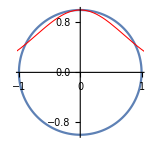

```mathematica
Show[p2,p1]
```

```mathematica
h[z_]=Exp[-z^2]
```

ⅇ^(-z^2)

```mathematica
f[x_,y_]=h[z]/.z->(x+ⅈ y)
```

ⅇ^(-(x+ⅈ y)^2)

```mathematica
ComplexExpand[%]
```

ⅇ^(-x^2+y^2) Cos[2 x y]-ⅈ ⅇ^(-x^2+y^2) Sin[2 x y]

The function is accepted to be analytic for all real x and y. It meets the requirements of Cauchy’s theorem, and therefore the contour integral equals zero.

11.  f[z_]=1/(2 z-1)

```mathematica
ClearAll["Global`*"]
```

This one does not pass the analyticity sanity check. The curve is not smooth within the unit circle. Therefore the integral is not zero, it must be something else.

```mathematica
Range[-6,6];
```

```mathematica
Range[-2,2,0.5];
```

```mathematica
p1=Plot[1/(2 z-1),{z,-2,2},AspectRatio->0.2,AxesLabel->{"z","f[z]"},PlotStyle->{Red,Thickness[0.006]},Ticks->{{-2.,-1.5,-1.,-0.5,0.,0.5,1.,1.5,2.},{-2.,-1.5,-1.,-0.5,0.,0.5,1.,1.5,2.}},PlotRange->{{-2,2},{-2,2}}];
p2=ParametricPlot[{Re[ⅇ^(ⅈ t)],Im[ⅇ^(ⅈ t)]},{t,0,2π},ImageSize->150
];
```

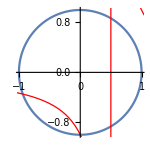

```mathematica
Show[p2,p1]
```

The problem function is

```mathematica
h[z_]=1/(2 z-1)
```

1/(-1+2 z)

and the equivalent in the complex plane is

```mathematica
f[x_,y_]=h[z]/.z->(x+ⅈ y)
```

1/(-1+2 (x+ⅈ y))

and the complex plane version still demonstrates the non-analytic point.

```mathematica
f[1/2,0]
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

The function is expanded.

```mathematica
ComplexExpand[1/(-1+2 (x+ⅈ y))]
```

-1/((-1+2 x)^2+4 y^2)+(2 x)/((-1+2 x)^2+4 y^2)-(2 ⅈ y)/((-1+2 x)^2+4 y^2)

The s.m. gets around the problem of discontinuity by using the method of deformation of path, an allowable method described on p. 656. Instead of allowing z to take on the value of 1/2, a new function, z(t)=1/2+ⅇ^(ⅈ t) is substituted, moving the unit circle away from the discontinuous point.

Note: The cells below in cyan do not apply directly to the problem, being only feel-good extra steps. Their relevance is explained in the cyan cells further down.

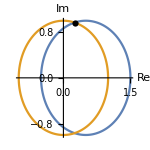

```mathematica
ParametricPlot[{{Re[1/2+ⅇ^(ⅈ t)],Im[ⅇ^(ⅈ t)]},{Re[ⅇ^(ⅈ t)],Im[ⅇ^(ⅈ t)]}},{t,0,2π},ImageSize->150,AxesLabel->{"Re","Im"},Epilog->{PointSize[0.03],Point[{0.25,0.968246}]}]
```

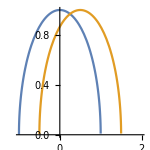

```mathematica
Plot[{√(1-x^2),√(1-(x-1/2)^2)},{x,-1,2},AspectRatio->Automatic,ImageSize->150]
```

```mathematica
Solve[√(1-x^2)-√(1-(x-1/2)^2)==0,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→1/4}}

```mathematica
N[√(1-(1/4)^2)]
```

0.968246

With the new z, the s.m. achieves the following

```mathematica
f[z_]=h[z]/.z->(1/2+ⅇ^(ⅈ t))
```

1/(-1+2 (1/2+ⅇ^(ⅈ t)))

Now comes an important addition to the procedure. This is use of numbered line (10) on page 647:

∫_C f[z]ⅆz=∫_a^b f[z[t]]z^·[t]ⅆt  where z^·[t]=D[z[t],t]

Incorporating the derivative of z into the contour integral. This derivative,

```mathematica
D[1/2+ⅇ^(ⅈ t),t]
```

ⅈ ⅇ^(ⅈ t)

turns the expression into

```mathematica
Integrate[(ⅈ ⅇ^(ⅈ t))/(-1+2 (1/2+ⅇ^(ⅈ t))),{t,0,2π}]
```

ⅈ π

Matching the answer in the text.

Integrating around the unit circle, it doesn’t matter where to start and finish, so the above green answer is valid. However, it feels a little better to make the shared point between original and new unit circles the start/end point.

```mathematica
z=0.25+ⅈ 0.9682458365518543
```

0.25+0.968246 ⅈ

```mathematica
ArcTan[0.9682458365518543/0.25]
```

1.31812

```mathematica
Integrate[(ⅈ ⅇ^(ⅈ t))/(-1+2 (1/2+ⅇ^(ⅈ t))),{t,0,1.318116071652818}]
```

0.+0.659058 ⅈ

```mathematica
Integrate[(ⅈ ⅇ^(ⅈ t))/(-1+2 (1/2+ⅇ^(ⅈ t))),{t,1.318116071652818,2π}]
```

0.+2.48253 ⅈ

```mathematica
0.659058035826409 ⅈ+2.4825346177633842 ⅈ
```

0.+3.14159 ⅈ

Repeating the answer obtained when integrating from 0 to 2 π.

13.  f[z_]=1/(z^4-1.1)

```mathematica
ClearAll["Global`*"]
```

```mathematica
p1=Plot[1/(z^4-1.1),{z,-2,2},AspectRatio->0.2,AxesLabel->{"z","f[z]"},PlotStyle->{Red,Thickness[0.003]},Ticks->{{-2.,-1.5,-1.,-0.5,0.,0.5,1.,1.5,2.},{-2.,-1.5,-1.,-0.5,0.,0.5,1.,1.5,2.}},PlotRange->{{-2,2},{-2,2}}];
```

```mathematica
p2=ParametricPlot[{Re[ⅇ^(ⅈ t)],Im[ⅇ^(ⅈ t)]},{t,0,2π},ImageSize->150
];
```

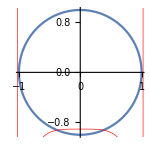

```mathematica
Show[p2,p1]
```

The problem instructions are to integrate on the unit circle. As it turns out, the closest points of discontinuity are exterior to the unit circle, and noting this fact avoids further calculations. It meets the requirements of Cauchy’s theorem, and therefore the contour integral equals zero.

15. f[z_] = Im[z]

```mathematica
ClearAll["Global`*"]
```

I’ll try this problem, which is not in the s.m., by following the ‘steps in applying theorem 2’ on p. 648:
(A) Represent the path C in the form z(t), (a ≤ t ≤ b).
(B) Calculate the derivative z^·(t) = dz/dt.
(C) Substitute z(t) for every z in f(z) (hence x(t) for x and y(t) for y).
(D) Integrate f[z(t)]z^·(t) over t from a to b.

Step (A). Looking at example 5 on p. 648, the path of the unit circle is represented as

```mathematica
z[t_]=Cos[t]+ⅈ Sin[t]
```

Cos[t]+ⅈ Sin[t]

Step (B). Calculate the derivative z^·(t)

```mathematica
devz=D[z[t],t]
```

ⅈ Cos[t]-Sin[t]

Step (C). Substitute z(t) for every z in f(z)

```mathematica
f[z_] = Im[z]/.z->(Cos[t]+ⅈ Sin[t])
```

Im[Cos[t]]+Re[Sin[t]]

Step (D). Integrate f[z(t)]z^·(t) over t from a to b.

```mathematica
Integrate[ f[z]devz,{t,0,2π}]
```

-π

The text answer is the same as the green cell above.

Belatedly, I check the analyticity,

```mathematica
u[x_,y_]=0
```

0

```mathematica
v[x_,y_]=y
```

y

```mathematica
D[u[x,y],x]
```

0

```mathematica
D[v[x,y],y]
```

1

The cyan cells are not equal, therefore the function is not analytic, and therefore Cauchy' s theorem cannot apply.

17.  f[z_]=1/(|z|^2)

```mathematica
ClearAll["Global`*"]
```

```mathematica
f[x_,y_]=1/Abs[x+y ⅈ]^2
```

1/Abs[x+ⅈ y]^2

```mathematica
ComplexExpand[%]
```

1/(x^2+y^2)

Since there is no imaginary component, it looks like D[v[x,y],y] will equal zero, whereas D[u[x,y],x] will not. So the function is not analytic. Skipping, then, the Cauchy Theorem option, I will go on to an attempted solution.

Having had luck the last problem, I will again try the ‘steps in applying theorem 2’ on p. 648:
(A) Represent the path C in the form z(t), (a ≤ t ≤ b).
(B) Calculate the derivative z^·(t) = dz/dt.
(C) Substitute z(t) for every z in f(z) (hence x(t) for x and y(t) for y).
(D) Integrate f[z(t)]z^·(t) over t from a to b.

Step (A). Looking at example 5 on p. 648, the path of the unit circle is represented as

```mathematica
z[t_]=ⅇ^(ⅈ t)
```

ⅇ^(ⅈ t)

(B) Calculate the derivative z^·(t) = dz/dt.

```mathematica
devz=D[z[t],t]
```

ⅈ ⅇ^(ⅈ t)

(C) Substitute z(t) for every z in f(z) (hence x(t) for x and y(t) for y).

```mathematica
f[z[t]]=1/(2 ⅇ^(2 ⅈ t))
```

1/2 ⅇ^(-2 ⅈ t)

(D) Integrate f[z(t)]z^·(t) over t from a to b.

```mathematica
Integrate[ 1/2 ⅇ^(-2 ⅈ t)devz,{t,0,2π}]
```

0

The green cell matches the text answer. In this case the Exp version of f[z] worked, but the Trig version did not. In the last problem it was the reverse. In this problem a zero integral is encountered which, however, does not qualify for its zip status because of the Cauchy Theorem, but rather because of its innate zeroness.

19.  f[z_]=z^3 Cot[z]

```mathematica
ClearAll["Global`*"]
```

```mathematica
p1=Plot[z^3 Cot[z],{z,-6,6},AspectRatio->0.3,ImageSize->350,AxesLabel->{"z","f[z]"},PlotStyle->{Red,Thickness[0.005]}];
```

```mathematica
p2=ParametricPlot[{Re[ⅇ^(ⅈ t)],Im[ⅇ^(ⅈ t)]},{t,0,2π},ImageSize->150
];
```

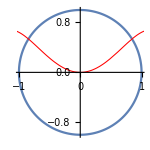

```mathematica
Show[p2,p1]
```

The plot shows that the problem function is well-behaved and has no discontinuities in the domain of interest.

```mathematica
f[z_]=z^3 Cot[z]
```

z^3 Cot[z]

```mathematica
f[x_,y_]=f[z]/.z->x+ⅈ y
```

(x+ⅈ y)^3 Cot[x+ⅈ y]

```mathematica
ComplexExpand[%];
```

```mathematica
u[x_,y_]=-(x^3 Sin[2 x])/(Cos[2 x]-Cosh[2 y])+(3 x y^2 Sin[2 x])/(Cos[2 x]-Cosh[2 y])-(3 x^2 y Sinh[2 y])/(Cos[2 x]-Cosh[2 y])+(y^3 Sinh[2 y])/(Cos[2 x]-Cosh[2 y]);
```

```mathematica
v[x_,y_]=-(3 x^2 y Sin[2 x])/(Cos[2 x]-Cosh[2 y])+(y^3 Sin[2 x])/(Cos[2 x]-Cosh[2 y])+(x^3 Sinh[2 y])/(Cos[2 x]-Cosh[2 y])-(3 x y^2 Sinh[2 y])/(Cos[2 x]-Cosh[2 y]);
```

```mathematica
PossibleZeroQ[D[u[x,y],x]-D[v[x,y],y]]
PossibleZeroQ[D[v[x,y],x]+D[u[x,y],y]]
```

True

True

It is seen above that the Cauchy-Riemann criteria are satisfied, therefore the value of the integral of the function around the unit circle is zero, in agreement with the text answer.

20 - 30 Further Contour Integrals
Evaluate the integral. Does Cauchy’s theorem apply?

21.  ∮1/(z-3 ⅈ)ⅆz , the circle |z|=π counterclockwise

```mathematica
ClearAll["Global`*"]
```

```mathematica
∮1/(z-3 ⅈ)ⅆz
```

I will first try the example 5 steps.
(A) Represent the path C in the form z(t), (a ≤ t ≤ b).
(B) Calculate the derivative z^·(t) = dz/dt.
(C) Substitute z(t) for every z in f(z) (hence x(t) for x and y(t) for y).
(D) Integrate f[z(t)]z^·(t) over t from a to b.

Step (A). Since z[t_]=ⅇ^(ⅈ t) is a unit circle, I suppose that π ⅇ^(ⅈ t) is a circle of radius π.

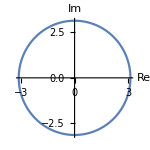

```mathematica
ParametricPlot[{Re[π ⅇ^(ⅈ t)],Im[π ⅇ^(ⅈ t)]},{t,0,2π},ImageSize->150,AxesLabel->{"Re","Im"}]
```

The plot looks okay as far as radius, I think.

```mathematica
z[t_]=π ⅇ^(ⅈ t)
```

ⅇ^(ⅈ t) π

Step (B).

```mathematica
devz=D[z[t],t]
```

ⅈ ⅇ^(ⅈ t) π

Step(C).

```mathematica
Integrate[1/(π ⅇ^(ⅈ t)-3 ⅈ)devz,{t,0,2π}]
```

2 ⅈ π

The green cell answer matches that of the text.

23.  ∮(2 z-1)/(z^2-z)ⅆz , counterclockwise around an ellipse with foci at origin and (2,0). Use partial fractions.

This problem is worked in the s.m.

```mathematica
ClearAll["Global`*"]
```

```mathematica
∮(2 z-1)/(z^2-z)ⅆz
```

ContourIntegral[(-1+2 z)/(-z+z^2),z]

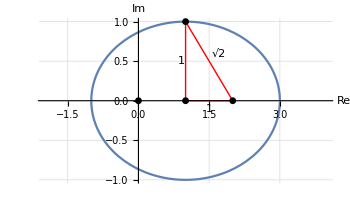

```mathematica
Plot[y/.Solve[((x-1)/2)^2+(y/1)^2==1],{x,-2,4},AspectRatio->Automatic,ImageSize->350,AxesLabel->{"Re","Im"},GridLines->Automatic,Epilog->{{Red,Line[{{1,0},{2,0}}]},{Text["1",{1.5,-0.1}]},{Red,Line[{{1,0},{1,1}}]},{Text["1",{0.9,0.5}]},{Red,Line[{{1,1},{2,0}}]},{Text["√2",{1.7,0.6}]},{PointSize[0.014],Point[{1,1}]},{PointSize[0.014],Point[{1,0}]},{PointSize[0.014],Point[{2,0}]},{PointSize[0.014],Point[{0,0}]}}]
```

The above plot displays an ellipse which satisfies the problem description. The problem is actually simple, provided example 6 on p. 656 is used, as pointed out by the s.m. The problem’s problem is that there are two points of discontinuity: 0 and 1. The hint to use partial fractions solves the issue by splitting the domain into two parts as shown schematically below. This schematic sketch represents two paths, each incorporating the dashed line, which will be added together.

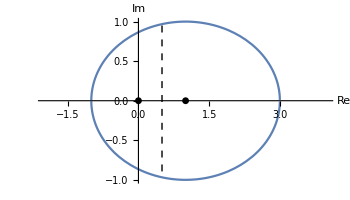

```mathematica
Plot[y/.Solve[((x-1)/2)^2+(y/1)^2==1],{x,-2,4},AspectRatio->Automatic,ImageSize->350,AxesLabel->{"Re","Im"},Epilog->{{Thick,Dashed,Line[{{0.5,0.95},{0.5,-0.95}}]},{PointSize[0.014],Point[{1,0}]},{PointSize[0.014],Point[{0,0}]}}]
```

The principle of deformation of path, illustrated in example 6 on p. 656, covers this situation nicely. It works because the problem function can be factored.

```mathematica
Factor[(2 z-1)/(z^2-z)]
```

(-1+2 z)/((-1+z) z)

```mathematica
Apart[%]
```

1/(-1+z)+1/z

```mathematica
egr1=(-1+z)^-1 (*note exponent of -1  *)
```

1/(-1+z)

```mathematica
egr2=z^-1  (*note exponent of -1  *)
```

1/z

Taking a look at numbered line (3) on p. 656,
∮ (z-z_0)^m ⅆz =Piecewise[{{2π ⅈ, m=-1}, {0, m≠-1 and integer}}]

The point z_0 is understood to be the point of discontinuity, and in the first factor is equal to 1.

```mathematica
ci1=∮ egr1 ⅆz==2π ⅈ
```

ContourIntegral[1/(-1+z),z]==2 ⅈ π

For this other factor of the function, the point z_0 is equal to 0.

```mathematica
ci2=∮ egr2 ⅆz==2π ⅈ
```

ContourIntegral[1/z,z]==2 ⅈ π

```mathematica
ci3==ci1+ci2==4π ⅈ
```

ci3==(ContourIntegral[1/(-1+z),z]==2 ⅈ π)+(ContourIntegral[1/z,z]==2 ⅈ π)==4 ⅈ π

Instead of taking a shortcut and strong-arming Mathematica into submission, there is a procedure on MathWorld under the heading Contour Integral, which could possibly be used to derive the answer more legitimately.

25.  ∮ⅇ^z/z ⅆz , C consists of |z|=2 counterclockwise and |z|=1 clockwise.

```mathematica
ClearAll["Global`*"]
```

```mathematica
(ⅇ^z/z)^-1
```

ⅇ^-z z

In the above form there are no values of z_0 which cause a discontinuity. The form that allows a discontinuity at z_0=0 is the form (ⅇ^z/z)^1, and then m=1, which means the integral equals 0. This answer agrees with the text.

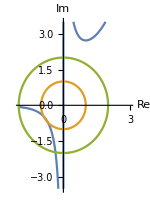

```mathematica
Plot[{ⅇ^x/x,y/.Solve[(x^2+y^2==1)],y/.Solve[(x^2+y^2==4)]},{x,-2,3},AspectRatio->Automatic,ImageSize->150,AxesLabel->{"Re","Im"},PlotRange->{-3.5,3.5}]
```

A plot of the annular domain and the candidate contour. The contour is not a closed path.

27.  ∮Cos[z]/z ⅆz , C consists of |z|=1 counterclockwise and |z|=3 clockwise.

```mathematica
ClearAll["Global`*"]
```

This time I’ll make the plot first.

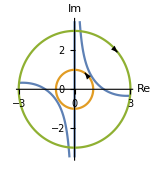

```mathematica
Plot[{Cos[x]/x,y/.Solve[(x^2+y^2==1)],y/.Solve[(x^2+y^2==9)]},{x,-3,3},AspectRatio->Automatic,ImageSize->150,AxesLabel->{"Re","Im"},PlotRange->{-3.5,3.5},Epilog->{{Arrowheads[.1],Arrow[{{2.1,2.1},{2.3,1.9}}]},{Arrowheads[.09],Arrow[{{0.7,0.67},{0.55,0.85}}]}}]
```

The above plot of the annular domain superimposed with candidate contour.

```mathematica
(Cos[z]/z)^-1==z/Cos[z]
```

True

So an alternate form of the current function is

```mathematica
(z/Cos[z])^-1
```

In the form shown above, the expression does admit of a discontinuity at the point z_0=π/2.  And the value π/2  is contained in the domain. However, I believe that because of the opposite orientation of the directions of the annuli, as shown by arrowheads, the integral will equal zero. A site with some treatment of this is:
http://www.math.unm.edu/~nitsche/courses/313/s16/lec19_int5.pdf. Also, the text, on p. 658, seems to reinforce this idea when talking about branch cuts. So this problem could end up equaling zero not through deformation of path and numbered line (3), but through calculation by means of branch cuts, one cut cutting out the point of discontinuity. I will skip the green cell coloring, though.

29.  ∮Sin[z]/(z+2 ⅈ z)ⅆz , C : |z-4-2 ⅈ|=5.5 clockwise.

```mathematica
ClearAll["Global`*"]
```

```mathematica
p1=Plot[ReIm[Sin[z]/(z+2 ⅈ z)],{z,-2,10},AspectRatio->1,ImageSize->200,AxesLabel->{"Re","Im"},PlotStyle->{Red,Thickness[0.003]},PlotRange->{{-2,10},{-0.5,0.5}}];
```

As Quora reminds me (https://www.quora.com/How-can-I-represent-circles-ellipses-parabolas-and-hyperbolas-using-complex-numbers), the equation of a complex circle can be expressed as |z - z_0| = r where z_0 is the center and r is the radius.
So in my former equation style, I would have

```mathematica
p2=ParametricPlot[{Re[5.5 ⅇ^(ⅈ t)+4],Im[5.5 ⅇ^(ⅈ t)+2ⅈ]},{t,0,2π},ImageSize->350,GridLines->Automatic
];
```

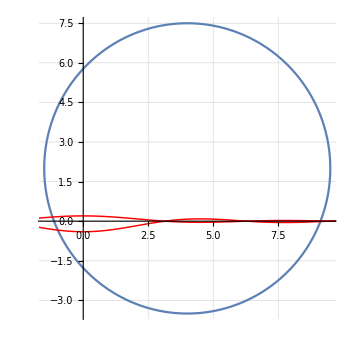

```mathematica
Show[p2,p1]
```

In the above plot it is seen that the problem function is continuous on the domain of interest. So I should be able to check the C-R criteria.

```mathematica
f[z_]=Sin[z]/(z+2 ⅈ z)
```

((1/5-(2 ⅈ)/5) Sin[z])/z

```mathematica
f[x_,y_]=f[z]/.z->x+ⅈ y
```

((1/5-(2 ⅈ)/5) Sin[x+ⅈ y])/(x+ⅈ y)

```mathematica
ComplexExpand[%];
```

```mathematica
u[x_,y_]=(x Cosh[y] Sin[x])/(5 (x^2+y^2))-(2 y Cosh[y] Sin[x])/(5 (x^2+y^2))+(2 x Cos[x] Sinh[y])/(5 (x^2+y^2))+(y Cos[x] Sinh[y])/(5 (x^2+y^2));
```

```mathematica
v[x_,y_]=-(2 x Cosh[y] Sin[x])/(5 (x^2+y^2))-(y Cosh[y] Sin[x])/(5 (x^2+y^2))+(x Cos[x] Sinh[y])/(5 (x^2+y^2))-(2 y Cos[x] Sinh[y])/(5 (x^2+y^2));
```

```mathematica
PossibleZeroQ[D[u[x,y],x]-D[v[x,y],y]]
PossibleZeroQ[D[v[x,y],x]+D[u[x,y],y]]
```

True

True

The C-R criteria being satisfied, the value of the integral around the path of interest is equal to zero.